Systems Cell Biology
Gene Networks: Homeostasis  
Copyright by Prof. Lee Bardwell, Univ. of California, Irvine

Your Name:  Samuel Morabito

# Bardwell Homework 1 Problem 3

Homeostasis of cellular tryptophan levels as regulated by the Trp Repressor in E. coli - a toy model.
(Note: a toy model is designed to illuminate principles without containing all the details or accurate estimates of rate constants).

"trpOut" is the concentration (in microMolar, uM) of tryptophan (trp) taken up by the cell from the outside environment.  This is assumed to be equal to the amount of trp in the outside environment.  For the first 10 minutes of the simulation, this number will be 10, and then at 10 seconds it changes to either 0, 5, 10 or 20 (because the cell swims into a new environment or the scientist changes the culture broth).  I use the Piecewise function to do this.

"trpMade" is the concentration of tryptophan (trp) synthesized by the cell.  Tryptophan is assumed to be used up/degraded as a first order process with a decay rate coefficient of d1.  Assuming (as we shall) that d1 =1, then at steady state

	total trp (inside the cell, in uM) = trpOut + trpMade 

The cell operates best when there is at least 10 uM total trp at steady state.
Cell's goals:  (G1) Don't let total trp levels fall below 10 uM; (G2) Don't waste energy synthesizing more trp than needed.
Thus, 
	(1)  When trpOut < 10, the cell should (ideally) make just enough trp to bring total trp up to 10.
	(2)  When trpOut > 10, the cell should (ideally) not make any trp.
	
Your goal:	
	Design a model that takes into account trp binding to and activating the Trp Repressor, and the Trp Repressor binding to and repressing the promoter of gene/protein Y.  Y is an enzyme that makes trp from an inexhaustible precursor substrate, according to the equation trpMade = kE Y[t], where kE is a rate constant.  (Note: The parameter we are calling kE is actually a combination of kcat, Km and the concentration of the precursor substrate, but we don't need to worry about that.)
	
	You should make a quasi-steady state approximation* for the action of trp on the Trp Repressor, and the binding of the Trp Repressor to DNA (as discussed in class).  All of this needs to be in one single equation for Y'[t].  More specifically, it needs to be in the input function, and not in the part that describes the decay of Y; you are not allowed to change the decay part of the equation.
	(* The approximation that some things happen much faster than others, e.g. trp binding to the trp repressor and trp repressor binding to DNA are fast relative to transcription*)
	
	Below I have used a very simple and not biologically realistic input function just to give you an example of a working notebook.  My input function is Pmax/(0.1 + trp[t]).  (The 0.1 in the denominator is there to prevent division by 0 when trp[t] = 0).  My input function actually works okay.  But it is not biologically realistic: a realistic input function should have some expression that represents the Trp Repressor binding to the promoter of Y, and trp binding to the Trp Repressor.  
	
ASSIGNED PROBLEMS
	3A.  Your task first task is to design a biologically realistic input function, based on what we've learned in class.
	3B.  Your second task is to chose parameters so that your biologically realistic input function works even better than my unrealistic one. That is, try to make the "Average Penalty" as close to zero as possible.  (Note that if the toy E. coli could not make its own trp, and was just at the whim of the environment, the Average Penalty would be 3.75; my Average Penalty is 2.3).  Do not change the decay parameters d1 and d2.  You can change every other parameter, and you will probably be adding parameters (such as Kd's and Hill numbers), but keep the d's = 1.  Keep all Hill numbers less than  or equal to 2  (Hill numbers of 1-4 are in the biologically realistic range, and there's no reason to suspect that any Hill numbers in the Trp Repressor system are greater than 2).
	3C.  Using the same input function as in 3A and 3B, what's the lowest Average Penalty you can get if there are no restrictions on Hill numbers?  Is there any striking difference in the dynamics when you compare the time courses for 3B to the time courses for  3C?  Again, keep the d's = 1.  Put these parameters in "otherParameters2".  Note, for 3B and 3C you do not need to exhaustively search all parameters nor find the optimal parameters.  Just try to find good ones.

```mathematica
ClearAll["Global`*"]

trpOut[time_]:=Piecewise[{{10, time<10},{trpOutValue, time≥10}}];
(* trpOut = 10 uM for first 10 min, then changes to trpOutValue *)
(* don't change this function *)

system ={ (* Trp Homeostasis Toy Model *)
trp'[t]==trpOut[t]+kE*Y[t]-d1*trp[t] (* don't change this equation *),

Y'[t]==(Pmax trp[t])/(k+trp[t])-d2*Y[t](* you may change the first half of this; indeed, you should.  Don't change the -d2*Y[t] part *)
};
```

```mathematica
initials = {Y[0]==0,trp[0]==10}; (* Don't change this *)
fullSystem = Join[system,initials]; (* Don't change this *)
```

```mathematica
decayParameters = {d1->1, d2->1};(* Don't change these *)
otherParameters = {Pmax->10, kE->5,k->100};(* Part B, you may change or add to these *)
otherParameters2 = {Pmax->10, kE->5,k->100} (* Part C, you may change or add to these *)

parameters = Join[decayParameters,otherParameters];

(* don't change anything else in this notebook *) 

case1=fullSystem/.parameters/.trpOutValue->0; (* red curve *)
case2=fullSystem/.parameters/.trpOutValue->5; (* blue curve *)
case3=fullSystem/.parameters/.trpOutValue->10; (* purple curve *)
case4=fullSystem/.parameters/.trpOutValue->20; (* green curve *)

solset1=NDSolve[case1,{Y[t], trp[t]}, {t,0,100}]; (* red curve *)
solset2=NDSolve[case2,{Y[t], trp[t]}, {t,0,100}]; (* blue curve *)
solset3=NDSolve[case3,{Y[t], trp[t]}, {t,0,100}]; (* purple curve *)
solset4=NDSolve[case4,{Y[t], trp[t]}, {t,0,100}]; (* green curve *)
```

{Pmax→10,kE→5,k→100}

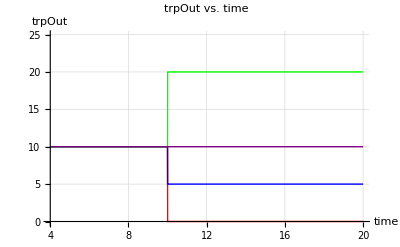

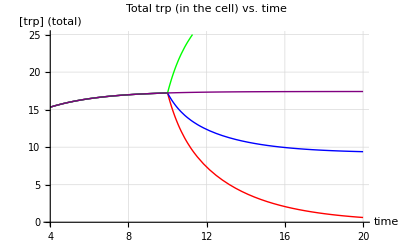

```mathematica
Plot[{
(trpOut[t]/.trpOutValue->0),
(trpOut[t]/.trpOutValue->5),
(trpOut[t]/.trpOutValue->20),
(trpOut[t]/.trpOutValue->10)}, 
{t, 4, 20}, PlotRange-> {-0.1,25},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Purple,Thick}},GridLines->Automatic,AxesLabel->{"time","trpOut"}, PlotLabel->"trpOut vs. time"] 

Plot[{trp[t]/.solset1,trp[t]/.solset2,trp[t]/.solset4,trp[t]/.solset3}, {t, 4, 20}, PlotRange-> {0,25}, PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Purple,Thick}},GridLines->Automatic,AxesLabel->{"time","[trp] (total)"}, PlotLabel->"Total trp (in the cell) vs. time"]
```

trpOut → 20, trpOut → 10, trpOut → 5, trpOut → 0

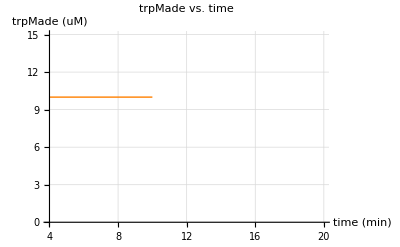

```mathematica
Plot[{kE*Y[t]/.solset1/.parameters,kE*Y[t]/.solset2/.parameters,kE*Y[t]/.solset4/.parameters,kE*Y[t]/.solset3/.parameters,trpOut[t]}, {t, 4, 20}, PlotRange-> {0,15}, PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Purple,Thick},{Orange,Thick}},GridLines->Automatic,AxesLabel->{"time (min)","trpMade (uM)"},PlotLabel->"trpMade vs. time"] 
(* plot all 4 curves on same graph *)
(* If two curves overlie then last one plotted is the one that's visible *)
(* That's why I'm plotting 10 mM trp last *)
(* Orange line on this graph shows TrpOut for first 10 minutes *)

(* trpOut -> 0, trpOut -> 5, trpOut -> 10, trpOut -> 20 *)
```

trpOut → 20, trpOut → 10, trpOut → 5, trpOut → 0

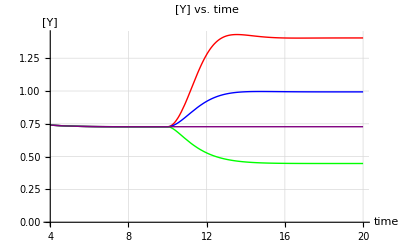

trpOut → 20, trpOut → 10, trpOut → 5, trpOut → 0

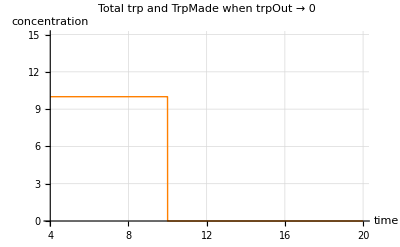

```mathematica
Plot[{trp[t]/.solset1,kE*Y[t]/.solset1/.parameters,trpOut[t]/.trpOutValue->0}, {t, 4, 20}, PlotRange-> {-0.1,15}, PlotStyle->{{Brown,Thick},{Magenta,Thick},{Orange, Thick}},GridLines->Automatic,AxesLabel->{"time","concentration"}, PlotLabel->"Total trp and TrpMade when trpOut → 0"]
```

Now let's calculate how well it worked:
(Note: The best possible average penalty is 0; If the toy E. coli could not make its own trp, and was just at the whim of the environment, the average penalty would be 3.75)

```mathematica
decayParameters = {d1->1, d2->1};(* Don't change these *)
otherParameters = {Pmax->10, kE->0.1,k->100};(* Part B, you may change or add to these *)
otherParameters2 = {Pmax->10, kE->0.1,k->100} (* Part C, you may change or add to these *)

parameters = Join[decayParameters,otherParameters];

(* don't change anything else in this notebook *) 

case1=fullSystem/.parameters/.trpOutValue->0; (* red curve *)
case2=fullSystem/.parameters/.trpOutValue->5; (* blue curve *)
case3=fullSystem/.parameters/.trpOutValue->10; (* purple curve *)
case4=fullSystem/.parameters/.trpOutValue->20; (* green curve *)

solset1=NDSolve[case1,{Y[t], trp[t]}, {t,0,100}]; (* red curve *)
solset2=NDSolve[case2,{Y[t], trp[t]}, {t,0,100}]; (* blue curve *)
solset3=NDSolve[case3,{Y[t], trp[t]}, {t,0,100}]; (* purple curve *)
solset4=NDSolve[case4,{Y[t], trp[t]}, {t,0,100}]; (* green curve *)

trp0=trp[t]/.solset1/.parameters/.t->100;
trp5=trp[t]/.solset2/.parameters/.t->100;
trp10=trp[t]/.solset3/.parameters/.t->100;
trp20=trp[t]/.solset4/.parameters/.t->100;

Print["TrpOut = 0; TrpMade =",trp0, " Total Trp =", trp0," Penalty =", Abs[10-trp0]]
Print["TrpOut = 5; TrpMade =",trp5-5, " Total Trp =", trp5," Penalty =", Abs[10-trp5]]
Print["TrpOut = 10; TrpMade =",trp10-10, " Total Trp =", trp10," Penalty =", trp10-10]
Print["TrpOut = 20; TrpMade =", trp20-20, " Total Trp =", trp20," Penalty =", trp20-20]
Print["Average Penalty = ",(Abs[10-trp0]+Abs[10-trp5]+(trp10-10)+(trp20-20))/4]
```

{Pmax→10,kE→0.1,k→100}

TrpOut = 0; TrpMade ={5.0063×10^-15} Total Trp ={5.0063×10^-15} Penalty ={10.}

TrpOut = 5; TrpMade ={0.0480547} Total Trp ={5.04805} Penalty ={4.95195}

TrpOut = 10; TrpMade ={0.091666} Total Trp ={10.0917} Penalty ={0.091666}

TrpOut = 20; TrpMade ={0.167831} Total Trp ={20.1678} Penalty ={0.167831}

Average Penalty = {3.80286}

Copyright by Prof. Lee Bardwell, Univ. of California, Irvine

To think about: If you think you've found a near-optimal set of parameters, consider this: The environment above is one where the cell often (50% of the time) finds itself without enough external trp, and only 25% of the time finds itself with more external trp than it needs.  If the environment changes, does the optimal parameter set change?

Some relevant papers (this list is in progress):
Bennett BD, Kimball EH, Gao M, Osterhout R, Van Dien SJ, Rabinowitz JD. Absolute metabolite concentrations and implied enzyme active site occupancy in Escherichia coli. Nat Chem Biol. 2009 Aug5(8):593-9
- says the intracellular concentration of tryptophan in a glucose-fed, exponentially-growing E. coli cell is 12 uM